#### 2.2 | Logistic Equation

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;β=2;
```

2 | Logistic Equation

```mathematica
q[t_]:= (q0*k)/((q0+(k-q0)*Exp[-β*t]))
```

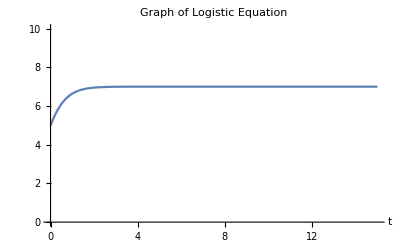

```mathematica
Plot[q[t],{t,0,15},PlotRange->{0,10},AxesLabel->Automatic,PlotLabel->"Graph of Logistic Equation"]
```